```mathematica
(*求解出精确解解*)
a[x_]:=If[0.4≤x≤0.6,1,0];
A=DSolve[D[u[x,t],t]+D[u[x,t],x]==0&&u[x,0]==a[x],u[x,t],{x,t}]
```

{{u[x,t]→If[0.4≤-t+x≤0.6,1,0]}}

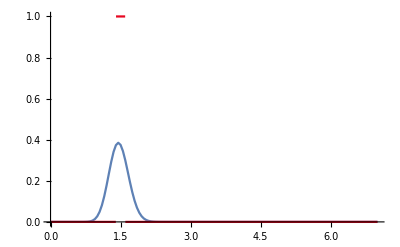
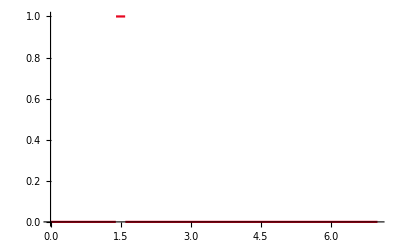

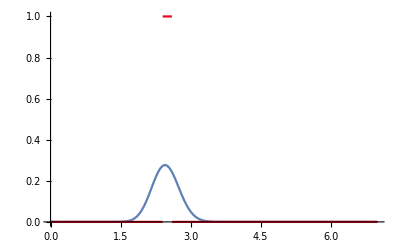
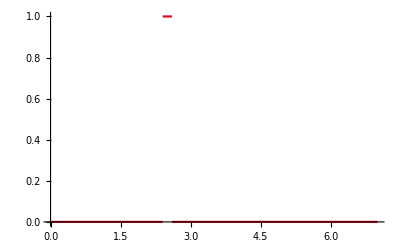

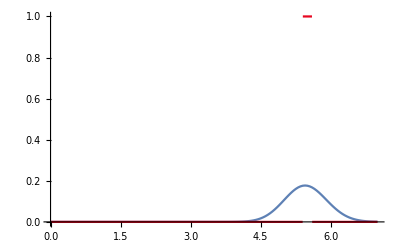
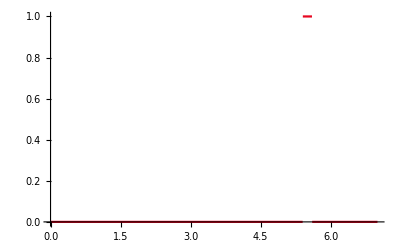

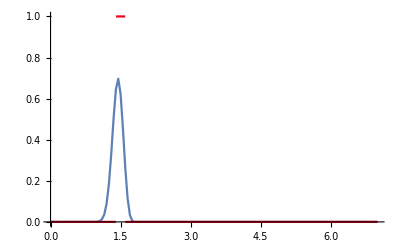
{-Graphics-,-Graphics-}

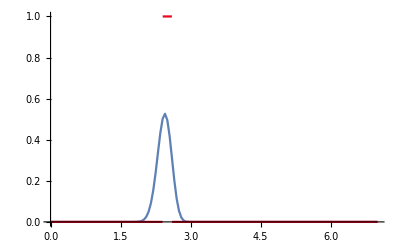
{-Graphics-,-Graphics-}

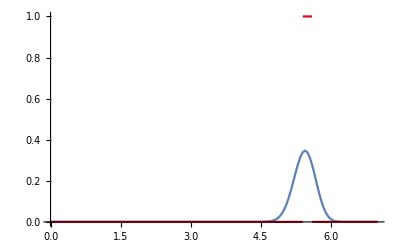
{-Graphics-,-Graphics-}

```mathematica
(*lambda=0.2*)
list=Import["E:\\study_materials\\PDEns\\05\\ns0.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-1],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
list=Import["E:\\study_materials\\PDEns\\05\\ns1.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-2],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
list=Import["E:\\study_materials\\PDEns\\05\\ns2.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-5],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
(*lambda=0.8*)
list=Import["E:\\study_materials\\PDEns\\05\\ns3.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-1],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
list=Import["E:\\study_materials\\PDEns\\05\\ns4.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-2],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
list=Import["E:\\study_materials\\PDEns\\05\\ns5.txt","Table"];
img0=ListLinePlot[list,PlotRange->All];
img=Plot[a[x-5],{x,0,7},PlotStyle->ColorData[3,"ColorList"]];
{Show[img0,img,PlotRange->All],img}
```